# A model for the LIT

We consider the Pöschl-Teller Hamiltonian
H=-1/2 d^2/(d x^2)-(λ (λ+1))/2 1/Cosh[x]^2
We consider the case λ=1, where there is a single bound state at E=-1/2

## Harmonic oscillator basis

```mathematica
ψ[n_,x_,b_:1]=1/(π^(1/4)√(b 2^n n!))HermiteH[n,x/b] Exp[-x^2/b^2/2]
```

(ⅇ^(-x^2/(2 b^2)) HermiteH[n,x/b])/(π^(1/4) √(2^n b n!))

### Quick calculation of matrix elements

Use generating function

```mathematica
Integrate[Exp[-x^2+2x t -t^2+2x s -s^2],{x,-∞,∞}]
```

ⅇ^(2 s t) √π

So 2^n/(n!)(st)^n. This shows that ⟨n|m⟩=δ_(n,m)

```mathematica
1/2 Integrate[D[Exp[-x^2/2+2x t -t^2], x]D[Exp[-x^2/2+2x s -s^2], x],{x,-∞,∞}]
```

1/4 ⅇ^(2 s t) √π (1-2 (s-t)^2)

```mathematica
FullSimplify[1/4 2^n/(n!)2^(-n/2)√(n!)2^(-(n+2)/2)√((n+2)!)ExpandAll[s^n t^n(1+2s t-2s^2-2t^2)/s^n/t^(n+2)]/.{s->0,t->∞},Assumptions->n∈PositiveIntegers]
```

-1/4 √((1+n) (2+n))

```mathematica
int=Simplify[1/4 2^(-n/2)√(n!)2^(-(n)/2)√((n)!)ExpandAll[(2^n/(n!)s^n t^n(1+2s t-2s^2-2t^2)+2^(n-1)/((n-1)!)s^(n-1) t^(n-1)(1+2s t-2s^2-2t^2))/s^n/t^(n)]]
```

-((-1+2 s^2-2 s t+2 t^2) (2 s t (-1+n)!+n!))/(8 s t (-1+n)!)

```mathematica
FullSimplify[Coefficient[Numerator[int],s t] s t /Denominator[int],Assumptions->n∈PositiveIntegers]
```

(1+n)/4

```mathematica
FullSimplify[1/4 2^(n-2)/((n-2)!)2^(-n/2)√(n!)2^(-(n-2)/2)√((n-2)!)ExpandAll[s^(n-2) t^(n-2)(1+2s t-2s^2-2t^2)/s^n/t^(n-2)]/.{s->∞,t->0},Assumptions-> n∈PositiveIntegers∧ n>2]
```

-1/4 √((-1+n) n)

So 1/42^n/(n!)(s t)^n(1+2st -2 s^2-2 t^2).
So ⟨n|p^2|m⟩=Piecewise[{{1/4(2n+1), n=m}, {-1/4 √(n(n-1)), m=n-2}, {-1/4 √((n+1)(n+2)), m=n+2}}]

x matrix element

```mathematica
Integrate[x Exp[-x^2+2x t -t^2+2x s -s^2],{x,-∞,∞}]
```

ⅇ^(2 s t) √π (s+t)

```mathematica
ⅇ^(2 s t) √π (s+t)
```

ⅇ^(2 s t) √π (s+t)

```mathematica
FullSimplify[2^n/(n!)2^(-n/2)√(n!)2^(-(n+1)/2)√((n+1)!)ExpandAll[s^n t^n (s+t)/s^n/t^(n+1)]/.{s->0,t->∞},Assumptions->n∈PositiveIntegers]
```

(√(1+n))/(√2)

```mathematica
FullSimplify[2^(n-1)/((n-1)!)2^(-(n-1)/2)√(n!)2^(-(n)/2)√((n-1)!)ExpandAll[s^(n-1) t^(n-1) (s+t)/s^n/t^(n-1)]/.{t->0,s->∞},Assumptions->n∈PositiveIntegers∧ n>1]
```

(√n)/(√2)

### Define matrix elements needed

```mathematica
kin[n_,m_,b_:1]:=Piecewise[{{1/b^2 1/4(2n+1),n==m},{-1/4 1/b^2 √(n(n-1)),m==n-2},{-1/4 1/b^2 √((n+1)(n+2)),m==n+2}}]
```

```mathematica
V[m_,n_,b_:1]:=Block[{mm,nn},{mm,nn}=MinMax[{m,n}];V[mm,nn,b]=NIntegrate[ψ[mm,x,b]ψ[nn,x,b]1/Cosh[x]^2,{x,-∞,∞}]]
```

h calculates even parity eigenstates

```mathematica
h[mx_]:=Table[kin[n,m]- V[m,n],{m,0,mx,2},{n,0,mx,2}]
```

and h1 calculates odd parity eigenstates

```mathematica
h1[mx_]:=Table[kin[n,m]- V[m,n],{m,1,mx,2},{n,1,mx,2}]
```

matrix elements of x

```mathematica
h[mx_,b_]:=Table[kin[n,m,b]- V[m,n,b],{m,0,mx,2},{n,0,mx,2}]
```

```mathematica
h1[mx_,b_]:=Table[kin[n,m,b]- V[m,n,b],{m,1,mx,2},{n,1,mx,2}]
```

```mathematica
x[n_,m_,b_:1]:=Piecewise[{{b √(n/2),m==n-1},{b √((n+1)/2),m==n+1}}]
```

#### hosc basis, b=1

```mathematica
nbasis=50
```

50

```mathematica
evs=Eigensystem[h[nbasis]];
```

```mathematica
{ev0,evc0}=Sort[Transpose[evs],#1[[1]]<#2[[1]]&][[1]];ev0+0.5
```

4.89859×10^-9

```mathematica
rhs=Table[x[n-1,n] evc0[[n/2+1]],{n,2,nbasis,2}]+Table[x[n+1,n] evc0[[n/2+1]],{n,0,nbasis-2,2}];Norm[rhs]
```

0.906898

```mathematica
es=Eigensystem[h1[nbasis]];
```

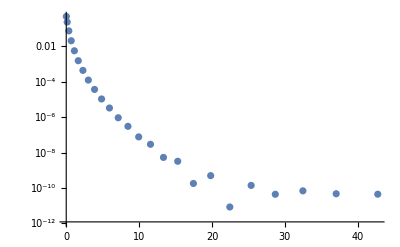

```mathematica
ListLogPlot[tb1={#[[1]],(#[[2]].rhs)^2}&/@Transpose[es]]
```

#### hosc basis, b=1/2

```mathematica
evs=Eigensystem[h[nbasis,1/2]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1975}. NIntegrate obtained 2.10152×10^-8 and 3.17418×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.42663}. NIntegrate obtained -1.02016×10^-8 and 6.69864×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.47353}. NIntegrate obtained 5.04571×10^-9 and 1.15085×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
{ev0,evc0}=Sort[Transpose[evs],#1[[1]]<#2[[1]]&][[1]];ev0+0.5
```

0.000141332

```mathematica
rhs=Table[x[n-1,n,1/2] evc0[[n/2+1]],{n,2,nbasis,2}]+Table[x[n+1,n,1/2] evc0[[n/2+1]],{n,0,nbasis-2,2}];Norm[rhs]
```

0.900112

```mathematica
es=Eigensystem[h1[nbasis,1/2]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.41518}. NIntegrate obtained -1.27079×10^-7 and 1.33327×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.39261}. NIntegrate obtained 6.12373×10^-8 and 2.49913×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.49766}. NIntegrate obtained -3.00808×10^-8 and 5.45761×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

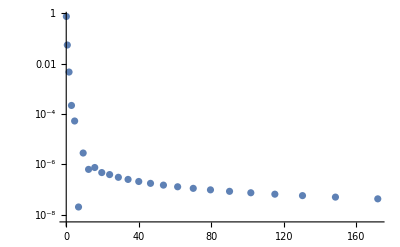

```mathematica
ListLogPlot[tb2={#[[1]],(#[[2]].rhs)^2}&/@Transpose[es]]
```

#### hosc basis, b=2

```mathematica
evs=Eigensystem[h[nbasis,2]];
```

```mathematica
{ev0,evc0}=Sort[Transpose[evs],#1[[1]]<#2[[1]]&][[1]];ev0+0.5
```

3.10334×10^-6

```mathematica
rhs=Table[x[n-1,n,2] evc0[[n/2+1]],{n,2,nbasis,2}]+Table[x[n+1,n,2] evc0[[n/2+1]],{n,0,nbasis-2,2}];Norm[rhs]
```

0.906913

```mathematica
es=Eigensystem[h1[nbasis,2]];
```

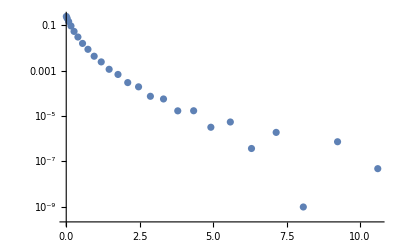

```mathematica
ListLogPlot[tb3={#[[1]],(#[[2]].rhs)^2}&/@Transpose[es]]
```

#### Gaussian basis

```mathematica
gaussian[s_,i_,n_]:=Table[(s^(1/4)i^((j-1)/4))/π^(1/4)Exp[-s i^(j-1)x^2/2],{j,1,n}]
```

```mathematica
gaussian1[s_,i_,n_]:=Table[(s^(3/4)i^((j-1)3/4))/(√2 π^(1/4))x Exp[-s i^(j-1)x^2/2],{j,1,n}]
```

```mathematica
g=gaussian[0.01,2,10];
```

```mathematica
norm=Integrate[Outer[Times,g,g],{x,-∞,∞}];
```

```mathematica
ham=1/2 Integrate[Outer[Times,D[g, x],D[g, x]],{x,-∞,∞}]-NIntegrate[Outer[Times,g,g/Cosh[x]^2],{x,-∞,∞}];
```

```mathematica
Eigenvalues[norm]
```

{7.605,1.81876,0.430277,0.108476,0.0279759,0.00717831,0.00179266,0.00042474,0.0000917122,0.0000168885}

```mathematica
Eigenvalues[{ham,norm}]
```

{9.61342,4.23564,1.96634,0.919492,-0.5,0.425305,0.191425,0.0809169,0.0291719,0.00642433}

```mathematica
{ev0,evc0}=Sort[Transpose[Eigensystem[{ham,norm}]],#1[[1]]<#2[[1]]&][[1]];ev0+0.5
```

4.76039×10^-10

```mathematica
g1=gaussian1[0.01,2,12];
```

```mathematica
norm1=Integrate[Outer[Times,g1,g1],{x,-∞,∞}];
```

```mathematica
ham1=1/2 Integrate[Outer[Times,D[g1, x],D[g1, x]],{x,-∞,∞}]-NIntegrate[Outer[Times,g1,g1/Cosh[x]^2],{x,-∞,∞}];
```

```mathematica
Eigenvalues[norm1]
```

{1.42684,0.853077,0.416649,0.182184,0.0747222,0.0293229,0.0110878,0.00404105,0.00141284,0.00046903,0.000145527,0.0000429033}

```mathematica
trans=NIntegrate[Outer[Times,g1, x g],{x,-∞,∞}];
```

```mathematica
evc0=evc0/Sqrt[evc0.(norm.evc0)];
```

```mathematica
rhs=trans.evc0;
```

```mathematica
rhs.Inverse[norm1].rhs
```

0.822467

```mathematica
ev1=Eigensystem[{ham1,norm1}];
```

```mathematica
new=#/Sqrt[#.norm1.#]&/@ev1[[2]];
```

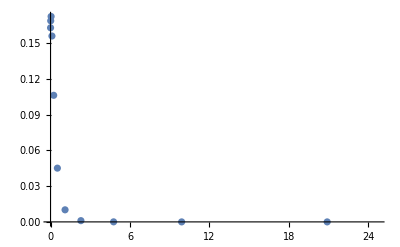

```mathematica
ListPlot[tb4=Transpose[{ev1[[1]],(#.rhs)^2&/@new}]]
```

#### Combined plots

```mathematica
ss[tb_]:=Transpose[{#[[1]],Accumulate[#[[2]]]}&[Transpose[Reverse[tb]]]]
```

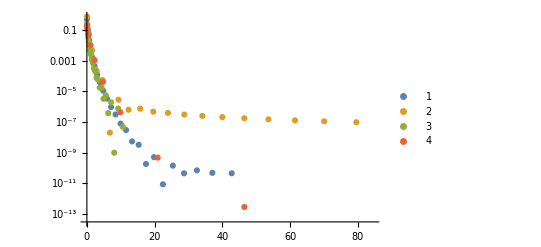

```mathematica
ListLogPlot[{tb1,tb2,tb3,tb4},PlotLegends->Automatic]
```

```mathematica
ss[tb_]:=Transpose[{#[[1]],Accumulate[#[[2]]]}&[Transpose[Reverse[tb]]]]
```

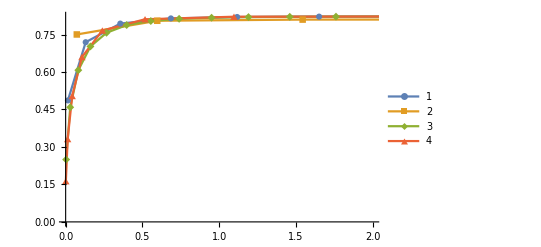

```mathematica
ListLinePlot[{ss[tb1],ss[tb2],ss[tb3],ss[tb4]},PlotMarkers->Automatic,PlotRange->{{0,2},All},PlotLegends->Automatic]
```

#### LIT

```mathematica
lit[tb_,w_]:=Plus@@((#[[2]])/(π w(1+(x-#[[1]])^2/w^2))&/@tb)
```

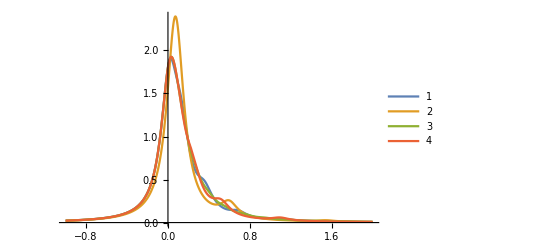

```mathematica
Plot[{lit[tb1,0.1],lit[tb2,0.1],lit[tb3,0.1],lit[tb4,0.1]},{x,-1,2},PlotRange->All,PlotLegends->Automatic]
```

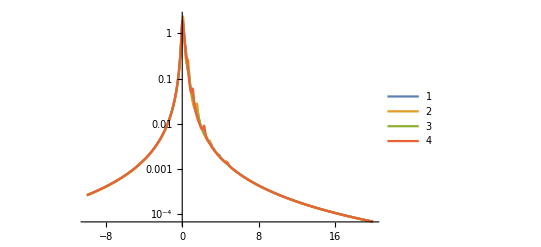

```mathematica
LogPlot[{lit[tb1,0.1],lit[tb2,0.1],lit[tb3,0.1],lit[tb4,0.1]},{x,-10,20},PlotRange->All,PlotLegends->Automatic]
```

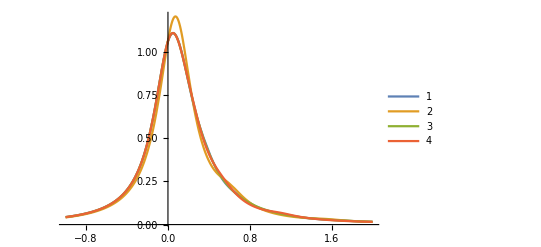

```mathematica
Plot[{lit[tb1,0.2],lit[tb2,0.2],lit[tb3,0.2],lit[tb4,0.2]},{x,-1,2},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Integrate[ Exp[-(x-x0)^2/w^2],{x,0,∞},Assumptions->w>0 ∧ x0>0]
```

1/2 √π w (1+Erf[x0/w])

```mathematica
strn[w_,x0_]=1/2 √π w (1+Erf[x0/w])
```

1/2 √π w (1+Erf[x0/w])

```mathematica
str[tb_,w_]:=Plus@@(#[[2]] Exp[-(x-#[[1]])^2/w^2]/strn[w,#[[1]]]&/@tb)
```

General::munfl: Exp[-182835.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-137270.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-105520.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

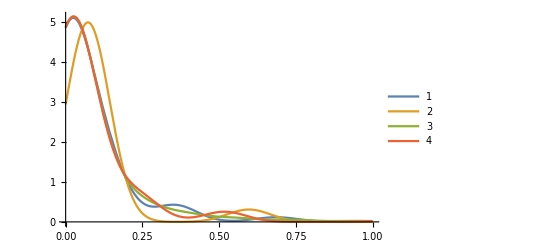

```mathematica
Plot[{str[tb1,0.1],str[tb2,0.1],str[tb3,0.1],str[tb4,0.1]},{x,0,1},PlotRange->All,PlotLegends->Automatic]
```

General::munfl: Exp[-182833.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-137269.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-105518.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

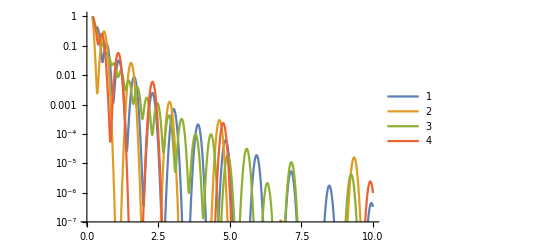

```mathematica
LogPlot[{str[tb1,0.1],str[tb2,0.1],str[tb3,0.1],str[tb4,0.1]},{x,0,10},PlotRange->{10^-7,1},PlotLegends->Automatic]
```

General::munfl: Exp[-45708.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-34317.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26379.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

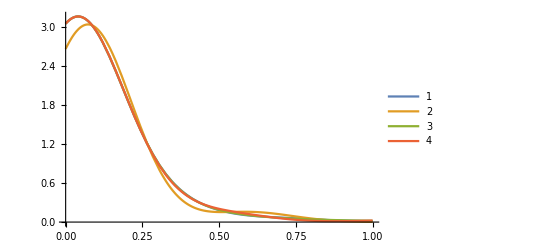

```mathematica
Plot[{str[tb1,0.2],str[tb2,0.2],str[tb3,0.2],str[tb4,0.2]},{x,0,1},PlotRange->All,PlotLegends->Automatic]
```

General::munfl: Exp[-11427.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8579.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6594.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

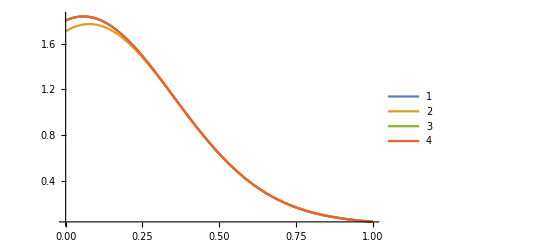

```mathematica
Plot[{str[tb1,0.4],str[tb2,0.4],str[tb3,0.4],str[tb4,0.4]},{x,0,1},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
str2[tb_,w_]:=Plus@@(#[[2]] Exp[-(x-#[[1]])^2/(w#[[1]])^2]/strn[w#[[1]],#[[1]]]&/@tb)
```

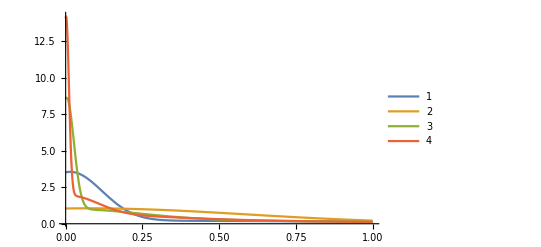

```mathematica
Plot[{str2[tb1,10],str2[tb2,10],str2[tb3,10],str2[tb4,10]},{x,0,1},PlotRange->All,PlotLegends->Automatic]
```